```mathematica
SetDirectory[NotebookDirectory[]];

boxLength=40;

iLattStart=1;
iLattEnd=100;
countsX={};
countsY={};
Do[
countsXtmp=Import["../data/lattice_v"<>IntegerString[iLatt,10,3]<>"/counts/X.txt","Table"];
countsYtmp=Import["../data/lattice_v"<>IntegerString[iLatt,10,3]<>"/counts/Y.txt","Table"];
If[countsXtmp[[-1,2]]≠0&&countsYtmp[[-1,2]]≠0,
AppendTo[countsX,countsXtmp];
AppendTo[countsY,countsYtmp];
,
Print["Not: "<>ToString[iLatt]];
];
,{iLatt,iLattStart,iLattEnd}];
countsX=Mean[countsX]//N;
countsY=Mean[countsY]//N;
pltData=Transpose[{countsX[[;;,2]],countsY[[;;,2]]}];
```

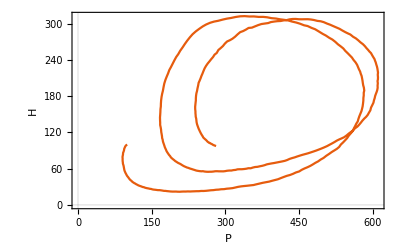

```mathematica
pltMean=ListLinePlot[pltData,FrameLabel->{"P","H"}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
If[!DirectoryQ["figures"],CreateDirectory["figures"]];
Export["figures/mean.pdf",pltMean]
```

figures/mean.pdf

```mathematica
fVals[times_,iLatt_]:=Module[{data1,data2,dataX1,dataX2,data11,data22,dataY1,dataY2},
data1=Import["../data/lattice_v"<>IntegerString[iLatt,10,3]<>"/lattice/"<>IntegerString[times[[1]],10,4]<>".txt","Table"];
data2=Import["../data/lattice_v"<>IntegerString[iLatt,10,3]<>"/lattice/"<>IntegerString[times[[2]],10,4]<>".txt","Table"];
dataX1=Select[data1,#[[3]]=="X"&][[;;,{1,2}]];
dataY1=Select[data1,#[[3]]=="Y"&][[;;,{1,2}]];
dataX2=Select[data2,#[[3]]=="X"&][[;;,{1,2}]];
dataY2=Select[data2,#[[3]]=="Y"&][[;;,{1,2}]];
Return[{{Length[dataX1],Length[dataX2]},{Length[dataY1],Length[dataY2]}}]
]
```

```mathematica
times={139,349};
vals={};
Do[
AppendTo[vals,fVals[times,iLatt]];
,{iLatt,1,100,1}];
dists=Map[Sqrt[Abs[#[[1,2]]-#[[1,1]]]^2+Abs[#[[2,2]]-#[[2,1]]]^2]&,vals];
```

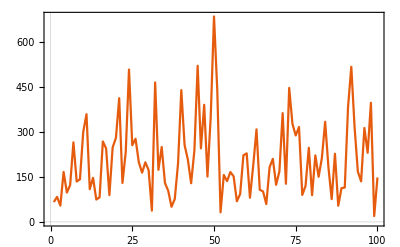

```mathematica
ListLinePlot[dists]
```

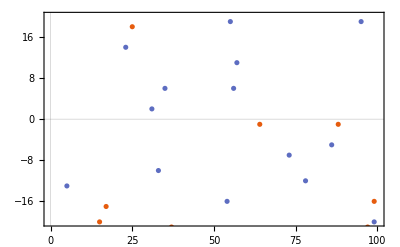
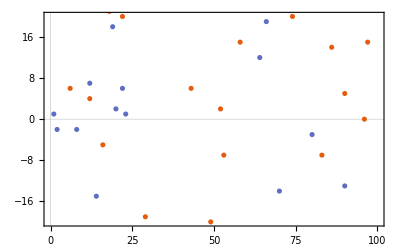

```mathematica
xtrue=560;
ytrue=125;
Row[{ListPlot[{vals[[;;,1,1]]-xtrue,vals[[;;,1,2]]-xtrue},PlotRange->{-20,20}],ListPlot[{vals[[;;,2,1]]-ytrue,vals[[;;,2,2]]-ytrue},PlotRange->{-20,20}]}]
```

```mathematica
vals[[31]]
```

{{535,562},{173,199}}

```mathematica
fMakePlot[time_,iLatt_]:=Module[{data1,dataX1,data11,dataY1},
data1=Import["../data/lattice_v"<>IntegerString[iLatt,10,3]<>"/lattice/"<>IntegerString[time,10,4]<>".txt","Table"];
dataX1=Select[data1,#[[3]]=="X"&][[;;,{1,2}]];
dataY1=Select[data1,#[[3]]=="Y"&][[;;,{1,2}]];
data11=ConstantArray[0,{boxLength,boxLength}];
Do[
data11[[pt[[1]],pt[[2]]]]=1;
,{pt,dataX1}];
Do[
data11[[pt[[1]],pt[[2]]]]=2;
,{pt,dataY1}];

Return[
ArrayPlot[data11,ImageSize->400,ColorRules->{0->White,1->Black,2->Blue}]]
];
```

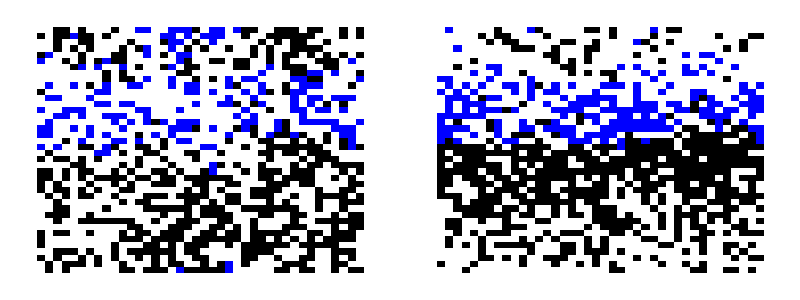

```mathematica
times={139,349};
lattV=31;
plts=Grid[{{fMakePlot[times[[1]],lattV],fMakePlot[times[[2]],lattV]}}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
If[!DirectoryQ["figures"],CreateDirectory["figures"]];
Export["figures/lattices.pdf",plts]
```

figures/lattices.pdf

```mathematica
times={139,349};
pltsMany={};
Do[
AppendTo[pltsMany,{}];
Do[
AppendTo[pltsMany[[-1]],fMakePlot[time,iLatt]];
,{time,times}];
,{iLatt,45,50}];
Grid[pltsMany]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-